## Lu163 - fit

## Experimental data

```mathematica
TSD1={{8.5,0.1966},{10.5,0.4597},{12.5,0.7746},{14.5,1.1609},{16.5,1.6112},{18.5,2.1265},{20.5,2.7051},{22.5,3.3441},{24.5,4.0411},{26.5,4.7937},{28.5,5.5992},{30.5,6.457},{32.5,7.3667},{34.5,8.3293},{36.5,9.3458},{38.5,10.4169},{40.5,11.5431},{42.5,12.7224},{44.5,13.9491},{46.5,15.2181},{48.5,16.5221}};
TSD2={{13.5,1.3394},{15.5,1.7467},{17.5,2.2184},{19.5,2.7527},{21.5,3.3484},{23.5,4.003},{25.5,4.7143},{27.5,5.4805},{29.5,6.3004},{31.5,7.1733},{33.5,8.0998},{35.5,9.08},{37.5,10.1147},{39.5,11.2036},{41.5,12.3466},{43.5,13.5441},{45.5,14.7911}};
TSD3={{16.5,2.1237},{18.5,2.6293},{20.5,3.1973},{22.5,3.8243},{24.5,4.5094},{26.5,5.2506},{28.5,6.0465},{30.5,6.8963},{32.5,7.7988},{34.5,8.7546},{36.5,9.7638},{38.5,10.8268},{40.5,11.9392},{42.5,13.0861}};
TSD4={{23.5,4.58},{25.5,5.2251},{27.5,5.9273},{29.5,6.6819},{31.5,7.4919},{33.5,8.3573},{35.5,9.2778},{37.5,10.2535},{39.5,11.2851},{41.5,12.3701}};
spins=Join[Table[TSD1[[i,1]],{i,1,Length[TSD1]}],Table[TSD2[[i,1]],{i,1,Length[TSD2]}],Table[TSD3[[i,1]],{i,1,Length[TSD3]}],Table[TSD4[[i,1]],{i,1,Length[TSD4]}]];
ExperimentalEnergies=Join[Table[TSD1[[i,2]],{i,1,Length[TSD1]}],Table[TSD2[[i,2]],{i,1,Length[TSD2]}],Table[TSD3[[i,2]],{i,1,Length[TSD3]}],Table[TSD4[[i,2]],{i,1,Length[TSD4]}]];
(*joint data - to be used in the fitting procedure*)
dataX=Join[Insert[#,1,1]&/@TSD1,Insert[#,2,1]&/@TSD2,Insert[#,3,1]&/@TSD3,Insert[#,4,1]&/@TSD4];
```

## reversed parameters X={1/ℐ_0,s}, where s=ℐ_0 V

## s is the scale factor

## Analytic formulas

```mathematica
moi[k_,β_,γ_]:=1/(1+(5/(16π))^(1/2)β)*(1-(5/(4π))^(1/2)β*Cos[γ*π/180+2/3 π*k]);(*moments of inertia without the inertia constant*)
a1p[β_,γ_]:=1/(2*moi[1,β,γ]);
a2p[β_,γ_]:=1/(2*moi[2,β,γ]);
a3p[β_,γ_]:=1/(2*moi[3,β,γ]);
```

```mathematica
b1[spin_,j_,β_,γ_,invi_,s_]:=-1(invi^2((2spin-1)(a3p[β,γ]-a1p[β,γ])+2j*a1p[β,γ])((2spin-1)(a2p[β,γ]-a1p[β,γ])+2j*a1p[β,γ])+8 invi^2*spin*j*a2p[β,γ]*a3p[β,γ]+invi^2((2j-1)(a3p[β,γ]-a1p[β,γ])+2spin*a1p[β,γ]+s*(2j-1)/(j(j+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]))((2j-1)(a2p[β,γ]-a1p[β,γ])+2spin*a1p[β,γ]+s*(2j-1)/(j(j+1))2 √3 Sin[γ*π/180]));
c1[spin_,j_,β_,γ_,invi_,s_]:=invi^4(((2spin-1)(a3p[β,γ]-a1p[β,γ])+2j*a1p[β,γ])((2j-1)(a3p[β,γ]-a1p[β,γ])+2spin*a1p[β,γ]+s*(2j-1)/(j(j+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]))-4spin*j*a3p[β,γ]^2)(((2spin-1)(a2p[β,γ]-a1p[β,γ])+2j*a1p[β,γ])((2j-1)(a2p[β,γ]-a1p[β,γ])+2spin*a1p[β,γ]+s*(2j-1)/(j(j+1))2 √3 Sin[γ*π/180])-4spin*j*a2p[β,γ]^2);
Omega1[spin_,j_,β_,γ_,invi_,s_]:=√(1/2(-b1[spin,j,β,γ,invi,s]+(b1[spin,j,β,γ,invi,s]^2-4c1[spin,j,β,γ,invi,s])^(1/2)));
Omega2[spin_,j_,β_,γ_,invi_,s_]:=√(1/2(-b1[spin,j,β,γ,invi,s]-(b1[spin,j,β,γ,invi,s]^2-4c1[spin,j,β,γ,invi,s])^(1/2)));
hMin[spin_,j_,β_,γ_,invi_,s_]:=invi*((spin+j)/2(a2p[β,γ]+a3p[β,γ])+a1p[β,γ](spin-j)^2-s*(2j-1)/(j+1)Sin[γ*π/180+π/6]);
```

## Analytical expressions - energies

```mathematica
energyExpression[n1_,n2_,spin_,j_,β_,γ_,invi_,s_]:=hMin[spin,j,β,γ,invi,s]+Omega1[spin,j,β,γ,invi,s]*(n1+1/2)+Omega2[spin,j,β,γ,invi,s]*(n2+1/2);
e0[β_,γ_,invi_,s_]:=energyExpression[0,0,6.5,6.5,β,γ,invi,s];
energyTSD1[spin_,β_,γ_,invi_,s_]:=If[Im[energyExpression[0,0,spin,6.5,β,γ,invi,s]-e0[β,γ,invi,s]]==0,energyExpression[0,0,spin,6.5,β,γ,invi,s]-e0[β,γ,invi,s],10^11];
energyTSD2[spin_,β_,γ_,invi_,s_]:=If[Im[energyExpression[1,0,spin-1,6.5,β,γ,invi,s]-e0[β,γ,invi,s]]==0,energyExpression[1,0,spin-1,6.5,β,γ,invi,s]-e0[β,γ,invi,s],10^11];
energyTSD3[spin_,β_,γ_,invi_,s_]:=If[Im[energyExpression[2,0,spin-2,6.5,β,γ,invi,s]-e0[β,γ,invi,s]]==0,energyExpression[2,0,spin-2,6.5,β,γ,invi,s]-e0[β,γ,invi,s],10^11];
energyTSD4[spin_,β_,γ_,invi_,s_]:=If[Im[energyExpression[3,0,spin-3,4.5,β,γ,invi,s]-e0[β,γ,invi,s]]==0,energyExpression[3,0,spin-3,4.5,β,γ,invi,s]-e0[β,γ,invi,s],10^10];
```

## Actual data fitting procedure

```mathematica
deformationParameters={0.38,17};
(*only `invi` and `s` are the free parameters. denoted by `a` and `b` in the fit*)
nlm=NonlinearModelFit[dataX,{Boole[id==1]*energyTSD1[x,deformationParameters[[1]],deformationParameters[[2]],a,b]+Boole[id==2]*energyTSD2[x,deformationParameters[[1]],deformationParameters[[2]],a,b]+Boole[id==3]*energyTSD3[x,deformationParameters[[1]],deformationParameters[[2]],a,b]+Boole[id==4]*energyTSD4[x,deformationParameters[[1]],deformationParameters[[2]],a,b],b>0},{a,b},{id,x}];
bestParameters=nlm["BestFitParameters"];
bestParameters
```

{a→0.0191488,b→0.00371989}

## Numerical results

```mathematica
tsd1Th=Table[energyTSD1[TSD1[[i,1]],deformationParameters[[1]],deformationParameters[[2]],Values@bestParameters[[1]],Values@bestParameters[[2]]],{i,1,Length[TSD1]}];
tsd2Th=Table[energyTSD2[TSD2[[i,1]],deformationParameters[[1]],deformationParameters[[2]],Values@bestParameters[[1]],Values@bestParameters[[2]]],{i,1,Length[TSD2]}];
tsd3Th=Table[energyTSD3[TSD3[[i,1]],deformationParameters[[1]],deformationParameters[[2]],Values@bestParameters[[1]],Values@bestParameters[[2]]],{i,1,Length[TSD3]}];
tsd4Th=Table[energyTSD4[TSD4[[i,1]],deformationParameters[[1]],deformationParameters[[2]],Values@bestParameters[[1]],Values@bestParameters[[2]]],{i,1,Length[TSD4]}];

(*theoretical data (pairs of spin-energy values) for plotting*)
TSD1Th=Table[{TSD1[[i,1]],tsd1Th[[i]]},{i,1,Length[TSD1]}];
TSD2Th=Table[{TSD2[[i,1]],tsd2Th[[i]]},{i,1,Length[TSD2]}];
TSD3Th=Table[{TSD3[[i,1]],tsd3Th[[i]]},{i,1,Length[TSD3]}];
TSD4Th=Table[{TSD4[[i,1]],tsd4Th[[i]]},{i,1,Length[TSD4]}];
(*array for calculating the RMS value *)
TheoreticalEnergies=Join[tsd1Th,tsd2Th,tsd3Th,tsd4Th];
```

## RMS calculation

theoretical energies deviation from the experimental results

```mathematica
RMS[expdata_,thdata_]:=√(Sum[(expdata[[i]]-thdata[[i]])^2,{i,1,Length[expdata]}]/(Length[expdata]+1));
```

```mathematica
RMS[ExperimentalEnergies,TheoreticalEnergies]
```

0.516138

## Graphical representation (theory vs. experiment)

## units: x-axis is the spin [ℏ] y-axis is the energy [MeV]

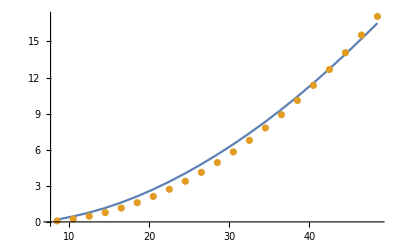

```mathematica
ListPlot[{TSD1,TSD1Th},Joined->{True,False}]
```

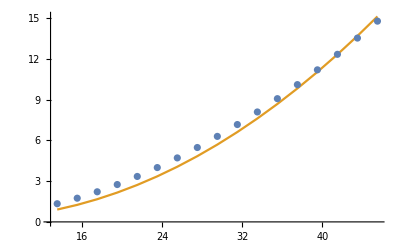

```mathematica
ListPlot[{TSD2,TSD2Th},Joined->{False,True}(*,PlotStyle->{{Red},{Black,Thick}},PlotMarkers->{{Automatic, Medium},None}*)]
```

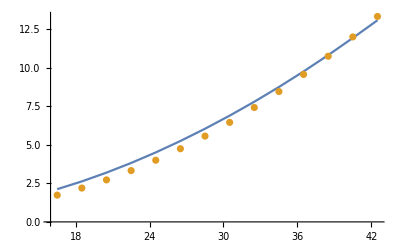

```mathematica
ListPlot[{TSD3,TSD3Th},Joined->{True,False}]
```

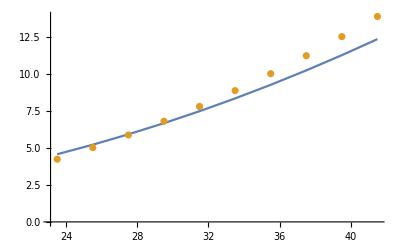

```mathematica
ListPlot[{TSD4,TSD4Th},Joined->{True,False}]
```